# 15. NALOGA: NEZNANI VRTEČI PREDMET

## REŠITEV

Najprej na vseh slikah posnetka seštejemo na primer 450. vrstico. Obračanje NVP-ja spreminja svetlost te vrstice.

```mathematica
Remove["Global`*"];

fps=60;
video=Video[NotebookDirectory[]<>"znani vrteči predmet.mp4"];


svetlosti=Norm/@VideoMapList[
	Total[ImageData[#Image][[450]]]&,
	video
];

Export[NotebookDirectory[]<>"svetlosti.h5",svetlosti];
```

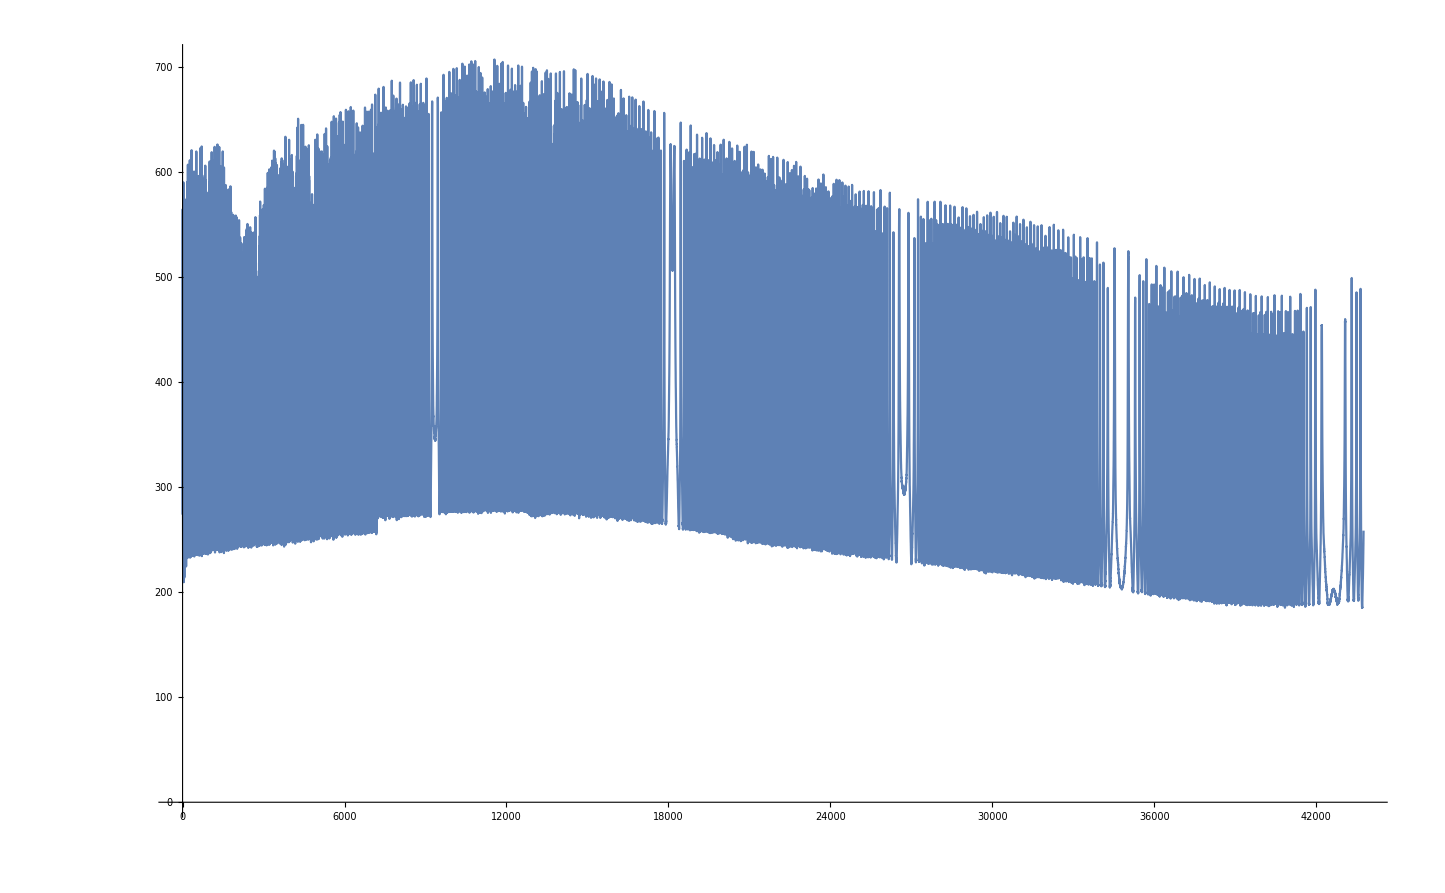
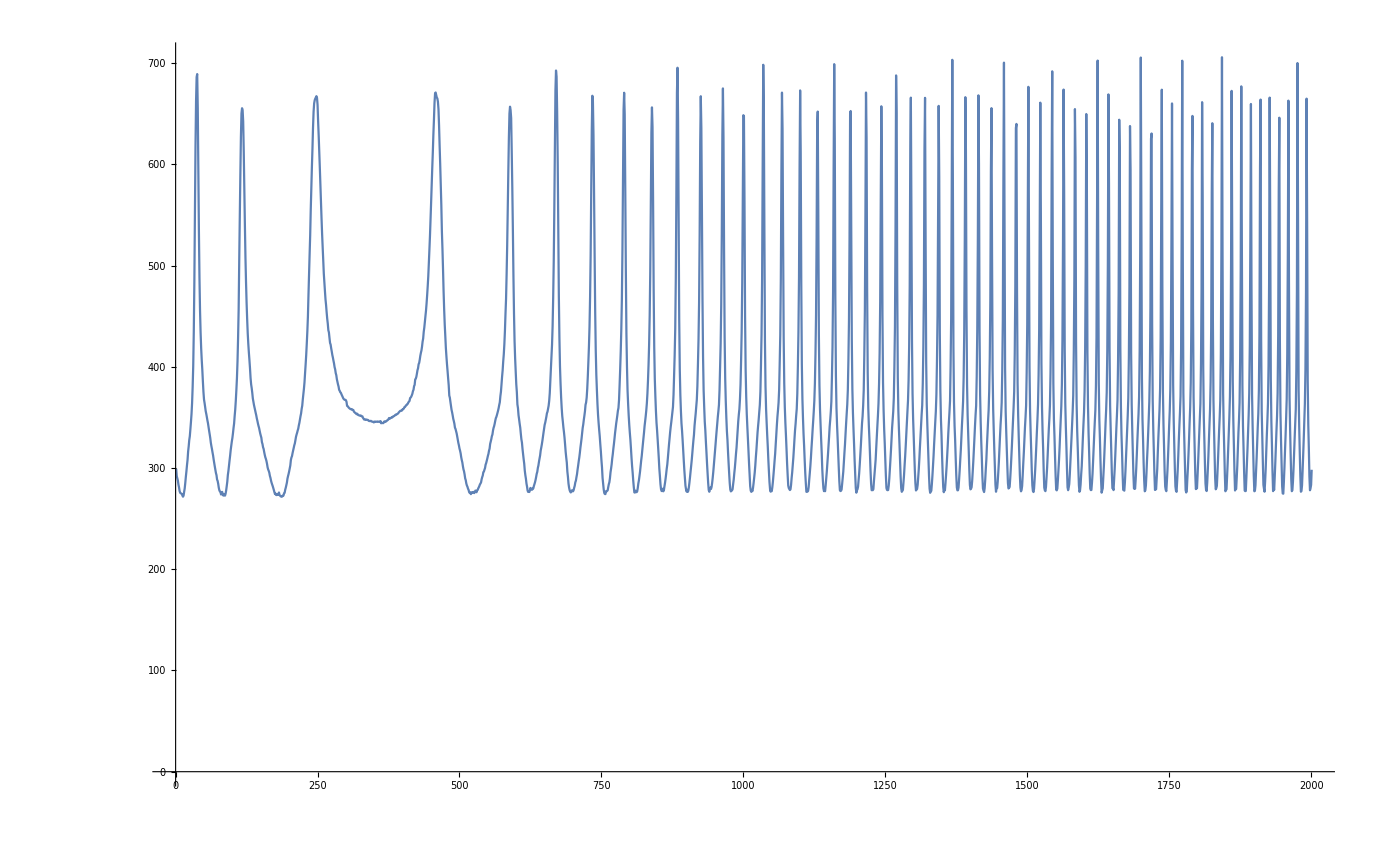

```mathematica
ListLinePlot[#]&/@{
	svetlosti,
	svetlosti[[9000;;11000]]
}
```

Poiščemo vrhove svetlosti. Te so 4 na obrat (ker je črni del NVP-ja kvadraten).

Narišemo graf zasuka φ[t]

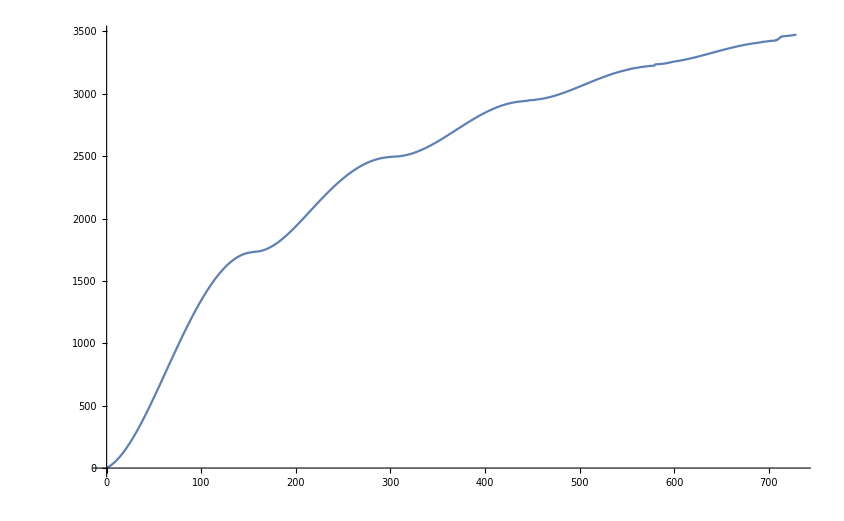

```mathematica
vrhoviIt=FindPeaks[svetlosti,2,InterpolationOrder->2][[;;,1]];
φodtji=Transpose[
	{tji,φji}={vrhoviIt/fps,N@Range@Length@vrhoviIt(2π)/4}
];

ListLinePlot@φodtji
```

Numerično odvajamo, dobimo kotne hitrosti

Iz grafa vidimo, da so zašumljene, zato čase zgladimo z LowpassFilter

Poiščemo vrhove zglajenih kotnih hitrosti

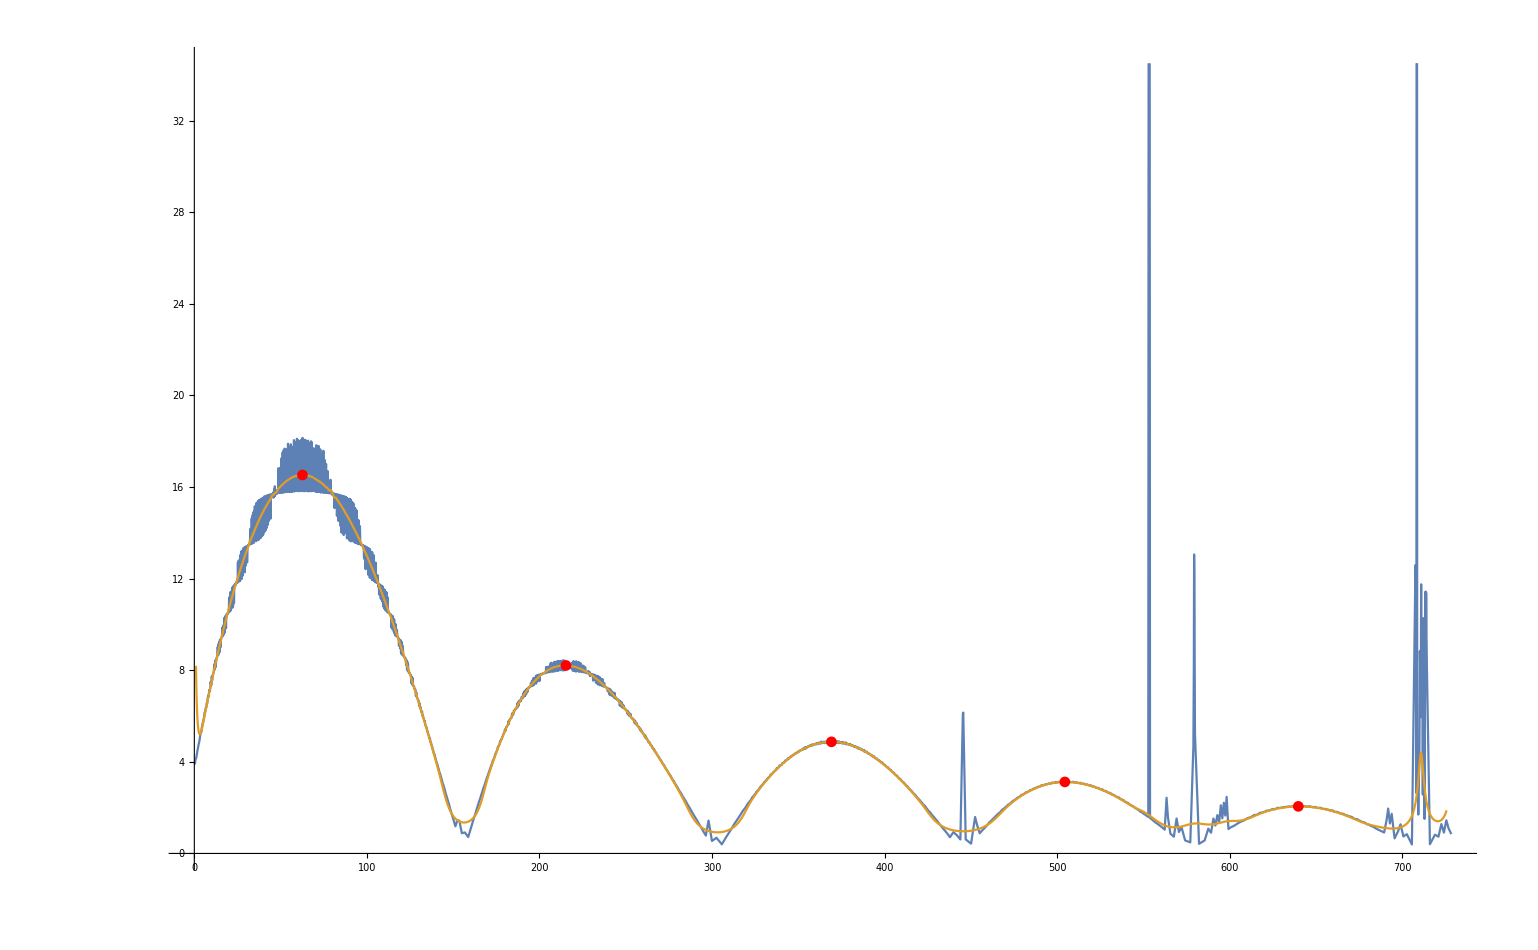

```mathematica
tjiGl1=LowpassFilter[tji,.2];
{ωji, ωjigl}=Transpose[{MovingAverage[#, 2], (Differences@φji)/(Differences@#)}]&/@{tji,tjiGl1};  

ωvrhovi=FindPeaks[ωjigl[[;;,2]],5,InterpolationOrder->2][[2;;-2]];
ωvrhoviPribližneTočke={tjiGl1[[Round@#]]&/@ωvrhovi[[;;,1]],ωvrhovi[[;;,2]]}ᵀ;

Show[
	ListLinePlot@{ωji, ωjigl},
	ListPlot[ωvrhoviPribližneTočke,PlotStyle->{Red,PointSize->.005}]
]
```

```mathematica
Total[ωvrhovi[[;;,2]]]
```

34.7836

```mathematica
15Round[%/15]
```

30